## Palm2015の実験結果の確認

```mathematica
Clear["Global`*"]
(*NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
```

plot2Doption

importData

jsonInfo

interpolateAndFourier

```mathematica
plot2Doption=Append[plot2Doption,{PlotStyle->{{Red},{Blue}}}];
plot2Doption=Append[plot2Doption,{GridLines->All}];
```

```mathematica
surgeExp=Import[FileNameJoin[{NotebookDirectory[],"surge.csv"}]];
tensionExp=Import[FileNameJoin[{NotebookDirectory[],"tension.csv"}]];
heaveExp=Import[FileNameJoin[{NotebookDirectory[],"heave.csv"}]];
pitchExp={#1,#2/180*π}&@@@Import[FileNameJoin[{NotebookDirectory[],"pitch.csv"}]];
waveelevationExp=Import[FileNameJoin[{NotebookDirectory[],"wave.csv"}]];
```

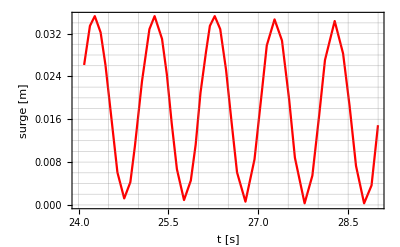
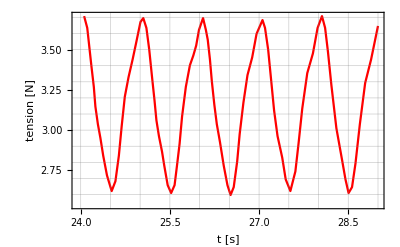
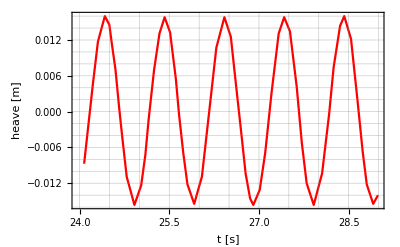
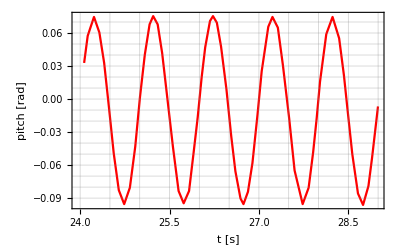
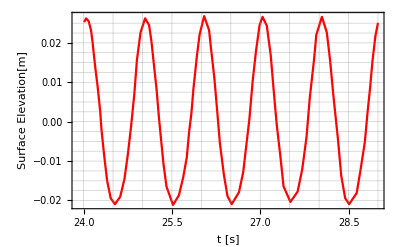

```mathematica
{ListPlot[surgeExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","surge [m]"}],
ListPlot[tensionExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","tension [N]"}],
ListPlot[heaveExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","heave [m]"}],
ListPlot[pitchExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}],
ListPlot[waveelevationExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","Surface Elevation[m]"}]}
```

## 2. 実験結果と数値計算の比較

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json

/Users/tomoaki/BEM/benchmark202405Palm2016/Palm2016_H0d08_T1d0_MESHwater_mod_DT0d025_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_without_mooring/result.json

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

no. | title | length

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(probe1_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(probe2_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(probe3_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::jsontokenmismatch: トークンnullからの「u」が想定されています．「a」が見付かりました．

Import::jsonhintposandchar: 行26:35812の文字「a」の近くでエラーが生じました

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(probe4_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::take: simulation_time/.$Failedの15から-1の位置が取れません．

Part::take: -6+(float_COM/.$Failed)⟦1;;All,1⟧の15から-1の位置が取れません．

Transpose::nmtx: {(simulation_time/.$Failed)⟦15;;All⟧,(-6+(float_COM/.$Failed)⟦1;;All,1⟧)⟦15;;All⟧}の最初の2個のレベルは転置できません．

Part::take: -6.+(float_COM/.$Failed)⟦1;;All,1⟧の15から-1の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Transpose::nmtx: {(simulation_time/.$Failed)⟦15;;All⟧,(-6.+(float_COM/.$Failed)⟦1;;All,1⟧)⟦15;;All⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot::lpn: {{{-15.4+﻿24.00179856,-0.00149443},{8.69353,0.00732016},{8.79065,0.014615},{8.87158,0.0164387},{8.96871,0.0133992},{9.04964,0.00732016},{9.14676,-0.00240628},{9.24928,-0.0127406},{9.36259,-0.0176039},{9.46511,-0.0145643},{9.54065,-0.00787741},{9.65935,0.00428065},{9.78345,0.0140071},{9.86978,0.0164387},«20»,{11.9957,0.0118794},{12.1144,0.000937183},{12.2115,-0.0100051},{12.3734,-0.0185157},{12.5029,-0.0133485},{12.6162,-0.00210233},{12.7133,0.00823202},{12.8752,0.0155268},{13.0155,0.00944782},{13.1234,-0.000278623},{13.2313,-0.0115248},{13.3662,-0.0185157},{13.4903,-0.0151722},{13.5982,-0.00392604}},«1»}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{-15.4+﻿24.00179856,-0.00149443},{8.69353,0.00732016},{8.79065,0.014615},{8.87158,0.0164387},{8.96871,0.0133992},{9.04964,0.00732016},{9.14676,-0.00240628},{9.24928,-0.0127406},{9.36259,-0.0176039},{9.46511,-0.0145643},{9.54065,-0.00787741},{9.65935,0.00428065},{9.78345,0.0140071},{9.86978,0.0164387},{9.99388,0.0121834},{10.0748,0.00549645},{10.1558,-0.00362209},{10.2421,-0.0121327},{10.3608,-0.0179078},{10.4741,-0.0142604},{10.555,-0.00757345},{10.636,0.00215299},{10.7277,0.00975177},{10.7924,0.014615},{10.8734,0.0164387},{10.9651,0.0140071},{11.0622,0.00640831},{11.154,-0.00331814},{11.2457,-0.0127406},{11.386,-0.0182118},{11.5371,-0.010309},{11.6612,0.00245694},{11.7421,0.0109676},{11.8716,0.0158308},{11.9957,0.0118794},{12.1144,0.000937183},{12.2115,-0.0100051},{12.3734,-0.0185157},{12.5029,-0.0133485},{12.6162,-0.00210233},{12.7133,0.00823202},{12.8752,0.0155268},{13.0155,0.00944782},{13.1234,-0.000278623},{13.2313,-0.0115248},{13.3662,-0.0185157},{13.4903,-0.0151722},{13.5982,-0.00392604}},Transpose[{(simulation_time/.$Failed)⟦15;;All⟧,(-6+(float_COM/.$Failed)⟦1;;All,1⟧)⟦15;;All⟧}]},PlotRange→{{0,20},Automatic},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}},FrameLabel→{t [s],surge [m]}]
ListPlot[{{{-15.4+﻿24.00268817,-0.0128977},{8.67527,-0.00853409},{8.74516,-0.00217045},{8.82312,0.00492045},{8.90645,0.0119205},{9.02204,0.0161932},{9.09731,0.0147386},{9.14032,0.0114659},{9.19946,0.00728409},{9.2586,0.00110227},{9.31237,-0.00398864},{9.38763,-0.0107159},{9.51667,-0.0154432},{9.62957,-0.0121705},{9.69946,-0.00707955},{9.75323,-0.00126136},{9.84462,0.00710227},{9.93602,0.0132841},{10.022,0.0160114},{10.1134,0.0134659},{10.2102,0.00564773},{10.264,-0.000352273},{10.3339,-0.00671591},{10.4038,-0.0119886},{10.5167,-0.0152614},{10.6457,-0.0107159},{10.7801,0.00128409},{10.8876,0.0109205},{11.022,0.0160114},{11.1296,0.0127386},{11.2156,0.00473864},{11.307,-0.003625},{11.3769,-0.0101705},{11.4522,-0.0143523},{11.5059,-0.0154432},{11.6134,-0.0128977},{11.7048,-0.00671591},{11.8124,0.00346591},{11.9306,0.0132841},{12.022,0.0160114},{12.1188,0.0136477},{12.2317,0.004375},{12.3177,-0.00507955},{12.3984,-0.0118068},{12.5167,-0.0154432},{12.6565,-0.0101705},{12.7747,-0.000170454},{12.85,0.00764773},{12.9575,0.0145568},{13.0274,0.0161932},{13.1403,0.012375},{13.2478,0.00219318},{13.3339,-0.00635227},{13.4038,-0.0119886},{13.5113,-0.0152614},{13.5919,-0.0138068}},Transpose[{simulation_time/.$Failed,-Mean[(float_COM/.$Failed)⟦1;;All,3⟧]+(float_COM/.$Failed)⟦1;;All,3⟧}]},PlotRange→{{0,20},Automatic},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}},FrameLabel→{t [s],heave [m]}]
ListPlot[{{{-15.4+﻿23.98662207,0.00807221},{8.66689,0.0408904},{8.72709,0.065504},{8.83244,0.0826589},{8.92274,0.0684875},{9.00301,0.0408904},{9.08328,0.000613536},{9.16355,-0.041155},{9.24883,-0.0747191},{9.33913,-0.0873988},{9.43445,-0.0724814},{9.52475,-0.0351881},{9.60502,0.0103098},{9.68528,0.048349},{9.76555,0.0759461},{9.82575,0.0834048},{9.901,0.0759461},{9.97625,0.0498408},{10.0666,0.00732634},{10.1569,-0.0351881},{10.2522,-0.0754649},{10.3375,-0.0866529},{10.4278,-0.0754649},{10.503,-0.041155},{10.5732,-0.00833687},{10.6385,0.0274648},{10.6987,0.0550618},{10.7789,0.0789296},{10.8291,0.0834048},{10.8943,0.0774379},{10.9645,0.0558077},{11.0548,0.0170226},{11.1351,-0.0254918},{11.2054,-0.0575641},{11.2906,-0.0821777},{11.3408,-0.0873988},{11.4161,-0.0762108},{11.4913,-0.0501054},{11.5766,-0.00609927},{11.6468,0.0334317},{11.7572,0.0737085},{11.8274,0.0826589},{11.9177,0.0729627},{12.003,0.0386528},{12.1084,-0.0098286},{12.1987,-0.0568182},{12.3341,-0.0873988},{12.4344,-0.0724814},{12.5097,-0.0404092},{12.5699,-0.00908274},{12.6251,0.0237354},{12.7304,0.0669957},{12.8358,0.0826589},{12.9462,0.0632664},{13.0264,0.0297024},{13.0916,-0.00386167},{13.1669,-0.0419009},{13.2622,-0.0777025},{13.3475,-0.0881447},{13.4378,-0.0709897},{13.498,-0.0456302},{13.5983,0.0013594}},Transpose[{simulation_time/.$Failed,-Mean[float_pitch/.$Failed]+(float_pitch/.$Failed)}]},PlotRange→{{0,20},All},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}},FrameLabel→{t [s],pitch [rad]}]
ListPlot[Transpose[{simulation_time/.$Failed,float_roll/.$Failed}],PlotRange→{{0,20},Automatic},Joined→True,PlotStyle→RGBColor[0, 0, 1],{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}},FrameLabel→{t [s],roll [rad]}]
ListPlot[Transpose[{simulation_time/.$Failed,float_yaw/.$Failed}],PlotRange→{{0,20},Automatic},Joined→True,PlotStyle→RGBColor[0, 0, 1],{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}},FrameLabel→{t [s],yaw [rad]}]
ListPlot[{{{8.60836,0.022274},{8.64178,0.0232174},{8.68635,0.0224627},{8.72535,0.0201986},{8.7532,0.016991},{8.77549,0.0137835},{8.79777,0.0107646},{8.83677,0.00604761},{8.88134,-0.000367486},{8.90362,-0.00508447},{8.94819,-0.0114996},{8.99833,-0.0179147},{9.05961,-0.022443},{9.13203,-0.0239524},{9.22117,-0.0220656},{9.29359,-0.0175373},{9.3493,-0.0114996},{9.40501,-0.00432975},{9.46072,0.00397214},{9.50529,0.0126514},{9.56657,0.0196325},{9.64457,0.0232174},{9.71142,0.0215193},{9.75042,0.017557},{9.78942,0.0120853},{9.83955,0.00510421},{9.87855,-0.00187692},{9.91755,-0.00791466},{9.95655,-0.0137637},{10.0067,-0.0194241},{10.1181,-0.0241411},{10.2184,-0.0216882},{10.2908,-0.0171599},{10.3521,-0.0120656},{10.3911,-0.0056505},{10.4301,-0.000933523},{10.4635,0.00510421},{10.5248,0.0137835},{10.5694,0.0190665},{10.6474,0.0237835},{10.7309,0.0201986},{10.7643,0.0154816},{10.8201,0.00812308},{10.8646,0.000387231},{10.9148,-0.00848069},{10.9816,-0.0164052},{11.0429,-0.0218769},{11.1153,-0.0239524},{11.2379,-0.0209335},{11.3103,-0.0158392},{11.366,-0.00866937},{11.4162,-0.00225428},{11.4719,0.00736836},{11.5276,0.0149155},{11.5889,0.0215193},{11.639,0.0235948},{11.7114,0.0213306},{11.7783,0.0137835},{11.8228,0.00585893},{11.8786,-0.00357503},{11.9454,-0.0122543},{11.9955,-0.0194241},{12.1125,-0.0233864},{12.2351,-0.0207448},{12.3131,-0.0150845},{12.3855,-0.00697126},{12.4412,0.00302874},{12.5136,0.0127457},{12.5526,0.0190665},{12.6474,0.0235948},{12.7309,0.0196325},{12.7866,0.0124627},{12.8423,0.00359478},{12.9203,-0.0075373},{12.976,-0.0167826},{13.0429,-0.022443},{13.1097,-0.0239524},{13.2379,-0.0211222},{13.2379,-0.0211222},{13.2992,-0.0156505},{13.3772,-0.00810333},{13.4217,-0.000744844},{13.4663,0.00567025},{13.5053,0.012274},{13.5554,0.0186891},{13.6,0.0220853}},Transpose[{simulation_time/.$Failed,-Mean[(probe2_intersection/.$Failed)⟦1;;All,3⟧]+(probe2_intersection/.$Failed)⟦1;;All,3⟧}]},PlotRange→{{0,20},Automatic},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}},FrameLabel→{t [s],wave elevation [m]}]

Transpose::nmtx: {simulation_time/.$Failed,-Mean[(probe1_intersection/.$Failed)⟦1;;All,3⟧]+(probe1_intersection/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Transpose::nmtx: {simulation_time/.$Failed,-Mean[(probe2_intersection/.$Failed)⟦1;;All,3⟧]+(probe2_intersection/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Transpose::nmtx: {simulation_time/.$Failed,-Mean[(probe3_intersection/.$Failed)⟦1;;All,3⟧]+(probe3_intersection/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

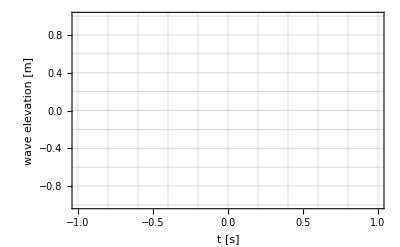

```mathematica
nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"
nameSim="/Users/tomoaki/BEM/benchmark202405Palm2016/Palm2016_H0d08_T1d0_MESHwater_mod_DT0d025_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_without_mooring/result.json"
(*nameSim="/Users/tomoaki/BEM/Palm2016_with_mooring_H0d04_T1d0/result.json"*)
(*nameSim="/Users/tomoaki/BEM/Palm2016_coarse_with_mooring_H0d04_T1d0/result.json"*)
(*nameSim="~/BEM/Palm2016_with_mooring/result.json"*)
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

probe1=importData[nameSim,"probe1_intersection"][[;;,3]];
probe1-=Mean[%];
probe2=importData[nameSim,"probe2_intersection"][[;;,3]];
probe2-=Mean[%];
probe3=importData[nameSim,"probe3_intersection"][[;;,3]];
probe3-=Mean[%];
probe4=importData[nameSim,"probe4_intersection"][[;;,3]];
probe4-=Mean[%];



istar=0;
shift=15.4;
maxtime=13;

Column@{ListPlot[{{#1-shift,#2-Mean[surgeExp[[;;,2]]]}&@@@surgeExp,Transpose@{time[[istar;;]],surgeSim[[istar;;]]}},
PlotRange->{{0,maxtime},Automatic},
Joined->True,Evaluate[plot2Doption],
FrameLabel->{"t [s]","surge [m]"}],
ListPlot[{{#1-shift,#2-Mean[heaveExp[[;;,2]]]}&@@@heaveExp,Transpose@{time,heaveSim-Mean[heaveSim]}},
PlotRange->{{0,maxtime},Automatic},
Joined->True,Evaluate[plot2Doption],
FrameLabel->{"t [s]","heave [m]"}],
ListPlot[{{#1-shift,#2-Mean[pitchExp[[;;,2]]]}&@@@pitchExp,Transpose@{time,pitchSim-Mean[pitchSim]}},
PlotRange->{{0,maxtime},All},
Joined->True,
Evaluate[plot2Doption],
FrameLabel->{"t [s]","pitch [rad]"}],
ListPlot[Transpose@{time,rollSim},
PlotRange->{{0,maxtime},Automatic},
Joined->True,
PlotStyle->Blue,
Evaluate[plot2Doption],
FrameLabel->{"t [s]","roll [rad]"}],
ListPlot[Transpose@{time,yawSim},
PlotRange->{{0,maxtime},Automatic},
Joined->True,
PlotStyle->Blue,
Evaluate[plot2Doption],
FrameLabel->{"t [s]","yaw [rad]"}],
ListPlot[{{#1-shift,#2-Mean[waveelevationExp[[;;,2]]]}&@@@waveelevationExp,Transpose@{time,probe2}},
PlotRange->{{0,maxtime},Automatic},
Joined->True,Evaluate[plot2Doption],
FrameLabel->{"t [s]","wave elevation [m]"}]}

ListPlot[{{time,probe1}ᵀ,{time,probe2}ᵀ,{time,probe3}ᵀ,{time,probe4}ᵀ}
,PlotStyle->{{Automatic,Dashed},{Thick,Red},{Automatic,Dashed},{Automatic,Dashed},{Automatic,Dashed}}
,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","wave elevation [m]"}]
```

### 2.2 フーリエ解析

```mathematica
ListPlot[{interpolateAndFourier[time[[istar;;]],surgeSim[[istar;;]]],
interpolateAndFourier[surgeExp[[2;;,1]],surgeExp[[2;;,2]]]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
ListPlot[{interpolateAndFourier[time,heaveSim-0.725],
interpolateAndFourier[heaveExp[[2;;,1]],heaveExp[[2;;,2]]]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
ListPlot[{interpolateAndFourier[time,pitchSim-Mean[pitchSim]],
interpolateAndFourier[pitchExp[[2;;,1]],pitchExp[[2;;,2]]]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
```

Part::take: simulation_time/.$Failedの15から-1の位置が取れません．

Part::take: -6+(float_COM/.$Failed)⟦1;;All,1⟧の15から-1の位置が取れません．

Part::take: -6.+(float_COM/.$Failed)⟦1;;All,1⟧の15から-1の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

ListPlot::lpn: {{},{{0.,0.036266},{0.203887,0.000577347},{0.407774,0.000164078},{0.611661,0.000220212},{0.815548,0.000023276},{1.01944,0.0172157},{1.22332,0.0000713783},{1.42721,0.0000690159},{1.6311,0.000153279},{1.83498,0.0000283671},{2.03887,0.000359552},{2.24276,0.000203445},{2.44664,0.0000366237},{2.65053,0.0000450401},{2.85442,0.0000775912},{3.05831,0.0000871309},{3.26219,0.0000994918},{3.46608,0.0000898785},{3.66997,0.0000843691},{3.87385,0.0000457607},{4.07774,0.000140503},{4.28163,0.0000440991},{4.48552,0.0000589631}}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{interpolateAndFourier[(simulation_time/.$Failed)⟦15;;All⟧,(-6+(float_COM/.$Failed)⟦1;;All,1⟧)⟦15;;All⟧],{{0.,0.036266},{0.203887,0.000577347},{0.407774,0.000164078},{0.611661,0.000220212},{0.815548,0.000023276},{1.01944,0.0172157},{1.22332,0.0000713783},{1.42721,0.0000690159},{1.6311,0.000153279},{1.83498,0.0000283671},{2.03887,0.000359552},{2.24276,0.000203445},{2.44664,0.0000366237},{2.65053,0.0000450401},{2.85442,0.0000775912},{3.05831,0.0000871309},{3.26219,0.0000994918},{3.46608,0.0000898785},{3.66997,0.0000843691},{3.87385,0.0000457607},{4.07774,0.000140503},{4.28163,0.0000440991},{4.48552,0.0000589631}}},PlotRange→{{0,5},All},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}}]

ListPlot::lpn: {{},{{0.,0.000203574},{0.20339,0.0000506119},{0.40678,0.0000279429},{0.610169,0.000173785},{0.813559,0.000120996},{1.01695,0.015827},{1.22034,0.0000240783},{1.42373,0.000168322},{1.62712,0.0000211095},{1.83051,0.0000789292},{2.0339,0.00038435},{2.23729,0.0000647511},{2.44068,0.0000632952},{«19»,«23»},{2.84746,«23»},{3.05085,0.000104285},{3.25424,0.0000599442},{3.45763,0.0000999468},{3.66102,0.0000392304},{3.86441,0.000102971},{4.0678,0.0000921123},{4.27119,0.0000691965},{4.47458,0.0000920589},{4.67797,0.0000662696},{4.88136,0.0000162314},{5.08475,6.89864×10^-6},{5.28814,0.0000778501}}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{interpolateAndFourier[simulation_time/.$Failed,-0.725+(float_COM/.$Failed)⟦1;;All,3⟧],{{0.,0.000203574},{0.20339,0.0000506119},{0.40678,0.0000279429},{0.610169,0.000173785},{0.813559,0.000120996},{1.01695,0.015827},{1.22034,0.0000240783},{1.42373,0.000168322},{1.62712,0.0000211095},{1.83051,0.0000789292},{2.0339,0.00038435},{2.23729,0.0000647511},{2.44068,0.0000632952},{2.64407,0.0000690504},{2.84746,0.0000899057},{3.05085,0.000104285},{3.25424,0.0000599442},{3.45763,0.0000999468},{3.66102,0.0000392304},{3.86441,0.000102971},{4.0678,0.0000921123},{4.27119,0.0000691965},{4.47458,0.0000920589},{4.67797,0.0000662696},{4.88136,0.0000162314},{5.08475,6.89864×10^-6},{5.28814,0.0000778501}}},PlotRange→{{0,5},All},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}}]

ListPlot::lpn: {{},{{0.,0.0189181},{0.202781,0.000455074},{0.405561,0.000125864},{0.608342,0.000533359},{0.811122,0.00115461},{1.0139,0.0850128},{1.21668,0.00122874},{1.41946,0.000887614},{1.62224,0.000481205},{1.82503,0.000170249},{2.02781,0.0012476},{2.23059,0.000618258},{2.43337,0.00039709},«4»,{3.44727,0.000366468},{3.65005,0.000593799},{3.85283,0.000226183},{4.05561,0.000187519},{4.25839,0.000221215},{4.46117,0.000283505},{4.66395,0.0000987442},{4.86673,0.000189096},{5.06952,0.000237893},{5.2723,0.000153501},{5.47508,0.00023443},{5.67786,0.000303029},{5.88064,0.0000749592}}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{interpolateAndFourier[simulation_time/.$Failed,-Mean[float_pitch/.$Failed]+(float_pitch/.$Failed)],{{0.,0.0189181},{0.202781,0.000455074},{0.405561,0.000125864},{0.608342,0.000533359},{0.811122,0.00115461},{1.0139,0.0850128},{1.21668,0.00122874},{1.41946,0.000887614},{1.62224,0.000481205},{1.82503,0.000170249},{2.02781,0.0012476},{2.23059,0.000618258},{2.43337,0.00039709},{2.63615,0.0000437523},{2.83893,0.000270335},{3.04171,0.000243859},{3.24449,0.000193582},{3.44727,0.000366468},{3.65005,0.000593799},{3.85283,0.000226183},{4.05561,0.000187519},{4.25839,0.000221215},{4.46117,0.000283505},{4.66395,0.0000987442},{4.86673,0.000189096},{5.06952,0.000237893},{5.2723,0.000153501},{5.47508,0.00023443},{5.67786,0.000303029},{5.88064,0.0000749592}}},PlotRange→{{0,5},All},Joined→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]],{PlotStyle→{{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1]}}},{GridLines→All}}]

## 係留ありとなしの比較（数値計算）

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_without_mooring/result.json

no. | title | length
1 | cpu_time | 1481
2 | float_COM | 1481
3 | float_EK | 1481
4 | float_EP | 1481
5 | float_accel | 1481
6 | float_area | 1481
7 | float_drag_force | 1481
8 | float_drag_torque | 1481
9 | float_force | 1481
10 | float_pitch | 1481
11 | float_roll | 1481
12 | float_torque | 1481
13 | float_velocity | 1481
14 | float_yaw | 1481
15 | probe1_intersection | 1481
16 | probe2_intersection | 1481
17 | probe3_intersection | 1481
18 | probe4_intersection | 1481
19 | simulation_time | 1481
20 | wall_clock_time | 1481
21 | water_E | 1481
22 | water_EK | 1481
23 | water_EP | 1481
24 | water_face_size | 1481
25 | water_point_size | 1481
26 | water_volume | 1481

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json

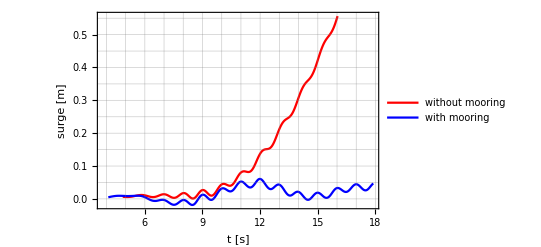
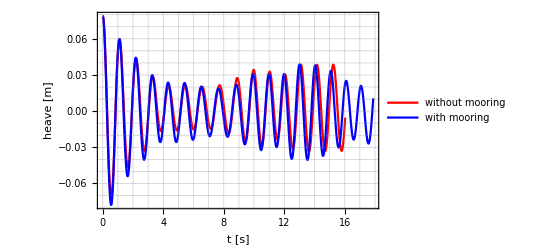
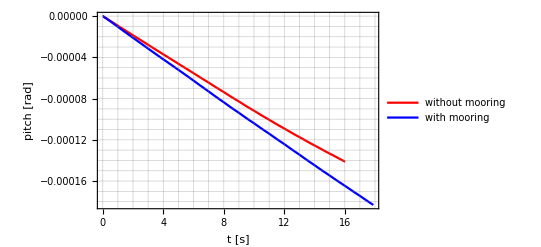
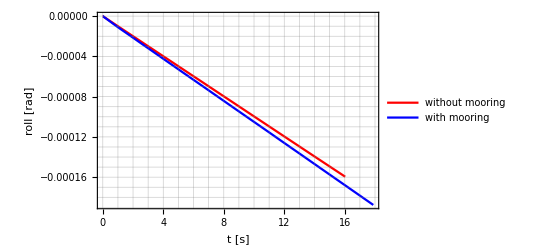
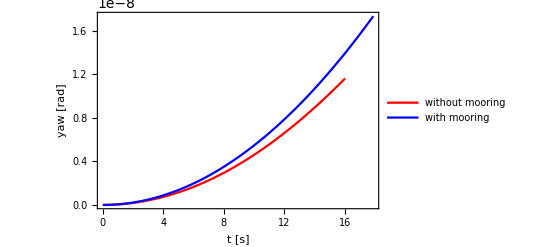

```mathematica
nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_without_mooring/result.json"

(*nameSim="~/BEM/Palm2016_with_mooring/result.json"*)
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"
timeMoor=importData[nameSim,"simulation_time"];
surgeSimMoor=importData[nameSim,"float_COM",1]-6;
heaveSimMoor=importData[nameSim,"float_COM",3];
forceSimMoor=importData[nameSim,"float_force"];
pitchSimMoor=importData[nameSim,"float_pitch"];
rollSimMoor=importData[nameSim,"float_roll"];
yawSimMoor=importData[nameSim,"float_yaw"];
torqueSimMoor=importData[nameSim,"float_torque"];

opt={PlotStyle->{Red,Blue},PlotLegends->{"without mooring","with mooring"}};
opt=AppendTo[opt,plot2Doption];

istart=400;

{ListPlot[{Transpose@{time[[istart;;]],surgeSim[[istart;;]]},Transpose@{timeMoor[[istart;;]],surgeSimMoor[[istart;;]]}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","surge [m]"}],
ListPlot[{Transpose@{time,heaveSim-0.725},Transpose@{timeMoor,heaveSimMoor-0.725}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","heave [m]"}],
ListPlot[{Transpose@{time,pitchSim},Transpose@{timeMoor,pitchSimMoor}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","pitch [rad]"}],
ListPlot[{Transpose@{time,rollSim},Transpose@{timeMoor,rollSimMoor}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","roll [rad]"}],
ListPlot[{Transpose@{time,yawSim},Transpose@{timeMoor,yawSimMoor}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","yaw [rad]"}]}
```

### 3.2 フーリエ解析

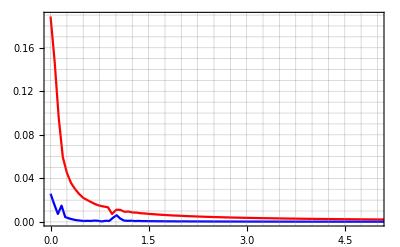

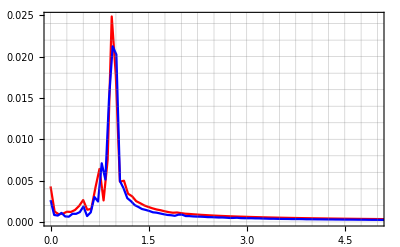

```mathematica
ListPlot[{
interpolateAndFourier[time[[istar;;]],surgeSim[[istar;;]]],
interpolateAndFourier[timeMoor[[istar;;]],surgeSimMoor[[istar;;]]]},
PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]

ListPlot[{
interpolateAndFourier[time,heaveSim-0.725],
interpolateAndFourier[timeMoor,heaveSimMoor-0.725]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
```